# Vector mode in D=5

```mathematica
t- Integrate[1/f[z],z]
```

t-∫1/f[z]ⅆz

```mathematica
(*z=1/r*)
X={v,z,x1,x2,x3};
```

```mathematica
d=5;
```

```mathematica
G=1/z^2{{-f[z] z^2,-1,ϵ 1/2 htx[z] E^(-I ω v+I k x3),(*ϵ 1/2 hty[z] E^(-I ω v+I k x3)*)0,0},{-1, 0,0,0,0},
{ϵ 1/2 htx[z] E^(-I ω v+I k x3),0,1,0,ϵ 1/2 hzx[z] E^(-I ω v+I k x3)},{(*ϵ 1/2 hty[z] E^(-I ω v+I k x3)*)0,0,0,1,(*ϵ 1/2 hzy[z] E^(-I ω (t- Integrate[1/f[z],z])+I k x3)*)0},{0,0,ϵ 1/2 hzx[z] E^(-I ω v+I k x3),(*ϵ 1/2 hzy[z] E^(-I ω v+I k x3)*)0,1}}(*/.ϵ->0*)(*/.z->1/r*);
```

```mathematica
G//MatrixForm
```

(-f[z] | -1/z^2 | (ⅇ^(ⅈ k x3-ⅈ v ω) ϵ htx[z])/(2 z^2) | 0 | 0
-1/z^2 | 0 | 0 | 0 | 0
(ⅇ^(ⅈ k x3-ⅈ v ω) ϵ htx[z])/(2 z^2) | 0 | 1/z^2 | 0 | (ⅇ^(ⅈ k x3-ⅈ v ω) ϵ hzx[z])/(2 z^2)
0 | 0 | 0 | 1/z^2 | 0
0 | 0 | (ⅇ^(ⅈ k x3-ⅈ v ω) ϵ hzx[z])/(2 z^2) | 0 | 1/z^2)

```mathematica
IG=Inverse[G];
IG/.ϵ->0//MatrixForm
```

(0 | -z^2 | 0 | 0 | 0
-z^2 | z^4 f[z] | 0 | 0 | 0
0 | 0 | z^2 | 0 | 0
0 | 0 | 0 | z^2 | 0
0 | 0 | 0 | 0 | z^2)

```mathematica
IG.G//Simplify
```

{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

```mathematica
Γ=Normal[Series[Table[1/2*Sum[IG[[i,l]]*(D[G[[j,l]],X[[k1]]]+D[G[[k1,l]],X[[j]]]-D[G[[j,k1]],X[[l]]]),{l,1,d}],{i,1,d},{j,1,d},{k1,1,d}],{ϵ,0,1}]];
```

```mathematica
Ric=Table[Sum[D[Γ[[k1,i,j]],X[[k1]]]-D[Γ[[k1,k1,i]],X[[j]]]+Sum[Γ[[q1,q1,k1]]Γ[[k1,i,j]]-Γ[[q1,i,k1]]Γ[[k1,q1,j]],{q1,1,d}],{k1,1,d}],{i,1,d},{j,1,d}](*Table[Sum[D[Γ[[i,j,k1]],X[[i]]]-D[Γ[[i,k1,i]],X[[j]]]+Sum[Γ[[i,i,p]]Γ[[p,j,k1]]-Γ[[i,j,p]]Γ[[p,i,k1]],{p,1,d}],{i,1,d}],{j,1,d},{k1,1,d}]*);
R=Normal[Series[Sum[IG[[i,j]]Ric[[i,j]],{i,1,d},{j,1,d}],{ϵ,0,1}]];
```

```mathematica
Ric//Dimensions
```

{5,5}

```mathematica
EinEq=Normal[Series[Ric+4 G,{ϵ,0,1}]]/.f->Function[z,1/z^2(1-z^4/zh^4)](*/.f->Function[z,1-z^4/zh^4]*)/.zh->1;
EinEq/.ϵ->0//Expand//Simplify//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

I output the three equations

```mathematica
EinEq[[1,3]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal(*//Collect[#,{htx'[z], hzx'[z]}]&*)
EinEq[[2,3]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal//Expand
EinEq[[3,5]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal(*//Collect[#,{htx'[z], hzx'[z]}]&*)
```

(ⅇ^(ⅈ (k x3-v ω)) ϵ (k^2 z htx[z]+k z ω hzx[z]+3 htx'[z]-3 z^4 htx'[z]-ⅈ z ω htx'[z]-z htx''[z]+z^5 htx''[z]))/(4 z)

(3 ⅇ^(ⅈ (k x3-v ω)) ϵ htx'[z])/(4 z)+1/4 ⅈ ⅇ^(ⅈ (k x3-v ω)) k ϵ hzx'[z]-1/4 ⅇ^(ⅈ (k x3-v ω)) ϵ htx''[z]

1/(4 z)ⅇ^(ⅈ (k x3-v ω)) ϵ (3 ⅈ k htx[z]+3 ⅈ ω hzx[z]-ⅈ k z htx'[z]+3 hzx'[z]+z^4 hzx'[z]-2 ⅈ z ω hzx'[z]-z hzx''[z]+z^5 hzx''[z])

I eliminate the second derivative of htx

```mathematica
htppRule=Solve[(EinEq[[2,3]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal//Expand)==0,htx''[z]]//Flatten
```

{htx''[z]→(3 htx'[z]+ⅈ k z hzx'[z])/z}

I look for differential equation for hzx and htx

```mathematica
Solve[{0==EinEq[[1,3]]/.htppRule[[1]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal,
0==EinEq[[3,5]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal},{hzx''[z],htx'[z]}]//Simplify
```

{{hzx''[z]→((k^3 z-3 ⅈ k ω) htx[z]+(k^2 z-3 ⅈ ω) ω hzx[z]+ⅈ (k^2 z (-1+z^4)+ω (3 ⅈ+ⅈ z^4+2 z ω)) hzx'[z])/(z (-1+z^4) ω),htx'[z]→(k (-ⅈ k htx[z]-ⅈ ω hzx[z]+(-1+z^4) hzx'[z]))/ω}}

The sln below is obtained solving for each of the component of EinEq

```mathematica
sln=Solve[{0==EinEq[[1,3]]/.htppRule[[1]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal,
0==EinEq[[3,5]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal},{hzx''[z],htx'[z]}]//Simplify//Flatten;
```

```mathematica
eqns=sln[[All,1]]-sln[[All,2]]
```

{-((k^3 z-3 ⅈ k ω) htx[z]+(k^2 z-3 ⅈ ω) ω hzx[z]+ⅈ (k^2 z (-1+z^4)+ω (3 ⅈ+ⅈ z^4+2 z ω)) hzx'[z])/(z (-1+z^4) ω)+hzx''[z],htx'[z]-(k (-ⅈ k htx[z]-ⅈ ω hzx[z]+(-1+z^4) hzx'[z]))/ω}

```mathematica
(*eqns={(k z ω htx[z]+(-1+z^4) (3 ⅈ ω hzx[z]+(3+z^4-2 ⅈ z ω) hzx'[z]))/(z (-1+z^4)^2)+hzx''[z],(k z ω hty[z]+(-1+z^4) (3 ⅈ ω hzy[z]+(3+z^4-2 ⅈ z ω) hzy'[z]))/(z (-1+z^4)^2)+hzy''[z],-(ⅈ ω htx[z])/(-1+z^4)+ⅈ k hzx[z]+htx'[z]-(k (-1+z^4) hzx'[z])/ω,-(ⅈ ω hty[z])/(-1+z^4)+ⅈ k hzy[z]+hty'[z]-(k (-1+z^4) hzy'[z])/ω};*)
```

### massless KG, equation

Doubt:how to know whit which order we start the expansion? Why htx and hty start from 1 and the pure spatial entries start from 0?

```mathematica
NHexpansion={htx->Function[z, Sum[c[1,i](1-z)^i,{i,0,3}]](*,hty->Function[z, Sum[c[2,i](1-z)^i,{i,1,3}]]*),hzx->Function[z, Sum[c[2,i](1-z)^i,{i,0,3}]](*,hzy->Function[z, Sum[c[4,i](1-z)^i,{i,0,3}]]*)};
```

```mathematica
(*2 constants.*)
replNH={c[1,1]->(ⅈ k (k c[1,0]+ω c[2,0]))/ω,c[2,1]->-(ⅈ (k^2-3 ⅈ ω) (k c[1,0]+ω c[2,0]))/(2 ω (2 ⅈ+ω)),c[1,2]->-(k (-12+k^2+3 ⅈ ω) (k c[1,0]+ω c[2,0]))/(4 ω (2 ⅈ+ω)),c[2,2]->((k^4+3 ω (-4 ⅈ+ω)) (k c[1,0]+ω c[2,0]))/(8 ω (2 ⅈ+ω) (4 ⅈ+ω)),c[1,3]->(k (-ⅈ k^4+6 k^2 (4 ⅈ+ω)+3 ⅈ (-64+28 ⅈ ω+ω^2)) (k c[1,0]+ω c[2,0]))/(24 ω (2 ⅈ+ω) (4 ⅈ+ω)),c[2,3]->((ⅈ k^6+3 k^2 (4+ⅈ ω) ω-3 k^4 (-4 ⅈ+ω)+3 ω (16+48 ⅈ ω+ω^2)) (k c[1,0]+ω c[2,0]))/(48 ω (2 ⅈ+ω) (4 ⅈ+ω) (6 ⅈ+ω))};
```

```mathematica
NI=3;
```

```mathematica
Normal[Series[{(1-z)^2(*,(1-z)^2,(1-z)*),(1-z)}eqns/.NHexpansion//.replNH,{z,1,NI}]]/.c[2,0]->c1//Simplify
```

{0,0}

```mathematica
Solve[0==Series[{(1-z)^2(*,(1-z)^2,(1-z)*),(1-z)}eqns/.NHexpansion//.replNH,{z,1,NI}]//Normal,Table[c[i,NI],{i,1,2}]]//Simplify
```

{{}}

```mathematica
UVexpansion={htx->Function[z, Sum[b[1,i] z^i,{i,0,8}]],hzx->Function[z, Sum[b[2,i] z^i,{i,0,8}]]};
```

```mathematica
(*4 constants in the UV (2 vevs and 2 sources), 2 constants in the IR and of course ω ---> total 7 constants. If we set all the sources to zero we are left with a total of 5 constants, oout of which 1 can be set to 1 using the linearity of the equations... so, effectively, we have 4 constants. But the problem requires 6 integration constants! Explanation: both sources will be non-zero up to gauge.*)sub={ b[1,0]->-czx ω/k(*, b[2,0]->-czy ω/k*), b[2,0]->czx(*, b[4,0]->czy*), b[1,4]->vzx,b[2,4]->-(vzx ω)/k(*, b[4,4]->vzy*)};
repl={b[1,1]->0,b[2,1]->-ⅈ (k b[1,0]+ω b[2,0]),b[1,2]->-1/4 k (k b[1,0]+ω b[2,0]),b[2,2]->-1/4 ω (k b[1,0]+ω b[2,0]),b[1,3]->1/6 ⅈ k ω (k b[1,0]+ω b[2,0]),b[2,3]->1/12 ⅈ (k^2-ω^2) (k b[1,0]+ω b[2,0]),b[1,5]->-4/5 ⅈ vzx ω,b[2,5]->-(ⅈ vzx (k^2-5 ω^2))/(5 k),b[1,6]->1/12 vzx (k^2-5 ω^2),b[2,6]->-1/4 k vzx ω+(7 vzx ω^3)/(12 k)}/.sub
```

{b[1,1]→0,b[2,1]→0,b[1,2]→0,b[2,2]→0,b[1,3]→0,b[2,3]→0,b[1,5]→-4/5 ⅈ vzx ω,b[2,5]→-(ⅈ vzx (k^2-5 ω^2))/(5 k),b[1,6]→1/12 vzx (k^2-5 ω^2),b[2,6]→-1/4 k vzx ω+(7 vzx ω^3)/(12 k)}

```mathematica
NN=0;
```

```mathematica
Normal[Series[{z,1}eqns/.UVexpansion/.sub/.repl,{z,0,NN}]]//Simplify
```

{0,0}

```mathematica
Solve[0==Series[{z,1}eqns/.UVexpansion/.repl(*/.sub*),{z,0,NN}]//Normal, Table[b[i,NN+1],{i,1,2}]]//Simplify
```

{}

```mathematica
Solve[{0==(Series[{z,1}eqns/.UVexpansion/.repl(*/.sub*),{z,0,3}]//Normal)[[1]],0==(Series[{z,1}eqns/.UVexpansion/.repl(*/.sub*),{z,0,3}]//Normal)[[2]]},Table[b[i,0],{i,1,2}]]
```

{}

```mathematica
0==(Series[{z,1}eqns/.UVexpansion/.repl(*/.sub*),{z,0,3}]//Normal)[[2]]
```

0==(ⅈ k (k b[1,0]+ω b[2,0]))/ω+z^3 (4 b[1,4]+(4 k b[2,4])/ω)

```mathematica
0==(ⅈ k (k b[1,0]+ω b[2,0]))/ω+z^3 (4 b[1,4]+(4 k b[2,4])/ω)/.b[1,0]->-(ω b[2,0])/k
```

0==z^3 (4 b[1,4]+(4 k b[2,4])/ω)

```mathematica
0==4 b[1,4]+(4 k b[2,4])/ω//Solve[#,b[2,4]]&
```

{{b[2,4]→-(ω b[1,4])/k}}

```mathematica
{{b[1,0]->-(ω b[2,0])/k}}
```

{{b[1,0]→-(ω b[2,0])/k}}

#### Constrains on sources

```mathematica
nc=5;
```

```mathematica
exponential=Exp[-I ω  v(*(t- Integrate[1/f[z],z])*)] ⅇ^(ⅈ k x3);
```

```mathematica
ξup=exponential ϵ{0ζ1+0Sum[ζζ1[j] z^j,{j,1,nc}],1/z (ζ2 +Sum[ζζ2[j] z^j,{j,1,nc}]),ζ3+Sum[ζζ3[j] z^j,{j,1,nc}], ζ4+Sum[ζζ4[j] z^j,{j,1,nc}], ζ5+Sum[ζζ5[j] z^j,{j,1,nc}]};
ξ=G.ξup;
```

```mathematica
ξup
```

{0,(ⅇ^(ⅈ k x3-ⅈ v ω) ϵ (ζ2+z ζζ2[1]+z^2 ζζ2[2]+z^3 ζζ2[3]+z^4 ζζ2[4]+z^5 ζζ2[5]))/z,ⅇ^(ⅈ k x3-ⅈ v ω) ϵ (ζ3+z ζζ3[1]+z^2 ζζ3[2]+z^3 ζζ3[3]+z^4 ζζ3[4]+z^5 ζζ3[5]),ⅇ^(ⅈ k x3-ⅈ v ω) ϵ (ζ4+z ζζ4[1]+z^2 ζζ4[2]+z^3 ζζ4[3]+z^4 ζζ4[4]+z^5 ζζ4[5]),ⅇ^(ⅈ k x3-ⅈ v ω) ϵ (ζ5+z ζζ5[1]+z^2 ζζ5[2]+z^3 ζζ5[3]+z^4 ζζ5[4]+z^5 ζζ5[5])}

```mathematica
Dξ=Table[1/2(D[ξ[[i]],X[[j]]]+D[ξ[[j]],X[[i]]])-Sum[Γ[[kk,i,j]] ξ[[kk]],{kk,1,5}],{i,1,5},{j,1,5}];
```

```mathematica
Dξ2=Table[(D[ξup[[j]],X[[i]]])+Sum[Γ[[j,i,kk]] ξup[[kk]],{kk,1,5}],{i,1,5},{j,1,5}];
```

```mathematica
subg={};
```

```mathematica
GG=Coefficient[Normal[Series[Simplify[2 Dξ]+G,{ϵ,0,1}]]/.f->Function[z,1-z^4/zh^4]/.zh->1,ϵ];
```

```mathematica
(**)Normal[Series[Simplify[1/exponential GG]/.f->Function[z,1-z^4/zh^4]/.zh->1/.UVexpansion/.sub/.repl,{z,0,2}]]/.l->1 /.{ζ4->(ⅈ czy)/(2 k),ζ3->(ⅈ czx)/(2 k),ζζ3[1]->(czx ω)/(2 k),ζζ4[1]->(czy ω)/(2 k),ζ5->0, ζ2->0,ζζ2[1]->0,ζζ5[1]->0,ζζ2[2]->0,ζζ2[3]->0,ζζ2[4]->0,ζζ5[2]->0,ζζ5[3]->0,ζζ3[2]->-(ⅈ czx ω^2)/(4 k),ζζ4[2]->-(ⅈ czy ω^2)/(4 k),ζζ3[3]->-(czx ω^3)/(12 k),ζζ4[3]->-(czy ω^3)/(12 k),ζζ2[5]->0,ζζ5[4]->0,ζζ5[5]->0,ζζ3[4]->(ⅈ czx ω^4)/(48 k),ζζ4[4]->(ⅈ czy ω^4)/(48 k),ζζ3[5]->(czx ω (24+ω^4))/(240 k),ζζ4[5]->(czy ω (24+ω^4))/(240 k)}//FullSimplify//Factor//MatrixForm
```

(0 | 0 | (24 k vzx z^3-24 ⅈ czx ω^2-12 czx z ω^3+4 ⅈ czx z^2 ω^4+czx z^3 ω^5)/(48 k z) | (czy ω (24-24 ⅈ z ω-12 z^2 ω^2+4 ⅈ z^3 ω^3+z^4 ω^4))/(48 k z^2) | 0
0 | 0 | (czx ω (24+24 z^4-24 ⅈ z ω-12 z^2 ω^2+4 ⅈ z^3 ω^3+z^4 ω^4))/(48 k z^2) | (czy ω (24+24 z^4-24 ⅈ z ω-12 z^2 ω^2+4 ⅈ z^3 ω^3+z^4 ω^4))/(48 k z^2) | 0
(24 k vzx z^3-24 ⅈ czx ω^2-12 czx z ω^3+4 ⅈ czx z^2 ω^4+czx z^3 ω^5)/(48 k z) | (czx ω (24+24 z^4-24 ⅈ z ω-12 z^2 ω^2+4 ⅈ z^3 ω^3+z^4 ω^4))/(48 k z^2) | 0 | 0 | -(ω (-24 ⅈ czx k+24 vzx z^3-12 czx k z ω+4 ⅈ czx k z^2 ω^2+czx k z^3 ω^3))/(48 k z)
(czy ω (24-24 ⅈ z ω-12 z^2 ω^2+4 ⅈ z^3 ω^3+z^4 ω^4))/(48 k z^2) | (czy ω (24+24 z^4-24 ⅈ z ω-12 z^2 ω^2+4 ⅈ z^3 ω^3+z^4 ω^4))/(48 k z^2) | 0 | 0 | -(czy (24-24 ⅈ z ω-12 z^2 ω^2+4 ⅈ z^3 ω^3+z^4 ω^4))/(48 z^2)
0 | 0 | -(ω (-24 ⅈ czx k+24 vzx z^3-12 czx k z ω+4 ⅈ czx k z^2 ω^2+czx k z^3 ω^3))/(48 k z) | -(czy (24-24 ⅈ z ω-12 z^2 ω^2+4 ⅈ z^3 ω^3+z^4 ω^4))/(48 z^2) | 0)

```mathematica
ξRules={ζ4->(ⅈ czy)/(2 k),ζ3->(ⅈ czx)/(2 k),ζζ3[1]->(czx ω)/(2 k),ζζ4[1]->(czy ω)/(2 k),ζ5->0, ζ2->0,ζζ2[1]->0,ζζ5[1]->0,ζζ2[2]->0,ζζ2[3]->0,ζζ2[4]->0,ζζ5[2]->0,ζζ5[3]->0,ζζ3[2]->-(ⅈ czx ω^2)/(4 k),ζζ4[2]->-(ⅈ czy ω^2)/(4 k),ζζ3[3]->-(czx ω^3)/(12 k),ζζ4[3]->-(czy ω^3)/(12 k),ζζ2[5]->0,ζζ5[4]->0,ζζ5[5]->0,ζζ3[4]->(ⅈ czx ω^4)/(48 k),ζζ4[4]->(ⅈ czy ω^4)/(48 k),ζζ3[5]->(czx ω (24+ω^4))/(240 k),ζζ4[5]->(czy ω (24+ω^4))/(240 k)};
```

```mathematica
ξup/.ξRules
```

{0,0,ⅇ^(ⅈ k x3-ⅈ v ω) ϵ ((ⅈ czx)/(2 k)+(czx z ω)/(2 k)-(ⅈ czx z^2 ω^2)/(4 k)-(czx z^3 ω^3)/(12 k)+(ⅈ czx z^4 ω^4)/(48 k)+(czx z^5 ω (24+ω^4))/(240 k)),ⅇ^(ⅈ k x3-ⅈ v ω) ϵ ((ⅈ czy)/(2 k)+(czy z ω)/(2 k)-(ⅈ czy z^2 ω^2)/(4 k)-(czy z^3 ω^3)/(12 k)+(ⅈ czy z^4 ω^4)/(48 k)+(czy z^5 ω (24+ω^4))/(240 k)),0}

```mathematica
vevTransformation={vzx->vzx-(czx ω^4)/24,vzy->vzy-(czy ω^4)/24};
```

```mathematica
(*both sources can be removed by a gauge transformation*)
Solve[{ζ4==(ⅈ czy)/(2 k),ζ3==(ⅈ czx)/(2 k)},{czy,czx}]
```

{{czy→-2 ⅈ k ζ4,czx→-2 ⅈ k ζ3}}

### Shooting Method

```mathematica
eqns
```

{-((k^3 z-3 ⅈ k ω) htx[z]+(k^2 z-3 ⅈ ω) ω hzx[z]+ⅈ (k^2 z (-1+z^4)+ω (3 ⅈ+ⅈ z^4+2 z ω)) hzx'[z])/(z (-1+z^4) ω)+hzx''[z],htx'[z]-(k (-ⅈ k htx[z]-ⅈ ω hzx[z]+(-1+z^4) hzx'[z]))/ω}

```mathematica
eqnlist[ω_,k_]:={-1/(z (-1+z^4) ω)((k^3 z-3 ⅈ k ω) htx[z]+(k^2 z-3 ⅈ ω) ω hzx[z]+ⅈ (k^2 z (-1+z^4)+ω (3 ⅈ+ⅈ z^4+2 z ω)) hzx'[z])+hzx''[z],htx'[z]-(k (-ⅈ k htx[z]-ⅈ ω hzx[z]+(-1+z^4) hzx'[z]))/ω};
```

```mathematica
(htx[z]/.NHexpansion/.replNH//.c[1,0]->c1//.c[2,0]->c2)//Collect[#,{  (1-z)},Simplify]&
(hzx[z]/.NHexpansion/.replNH/.c[1,0]->c1/.c[2,0]->c2)//Collect[#,{  (1-z)},Simplify]&
(htx[z]/.UVexpansion/.repl/. b[1,7]->0/. b[1,8]->0/.sub)//Collect[#,{  (z)},Simplify]&
(hzx[z]/.UVexpansion/.repl/. b[2,7]->0/. b[2,8]->0/.sub)//Collect[#,{  (z)},Simplify]&
```

c1+(ⅈ k (1-z) (c1 k+c2 ω))/ω-(k (1-z)^2 (-12+k^2+3 ⅈ ω) (c1 k+c2 ω))/(4 ω (2 ⅈ+ω))+(k (1-z)^3 (c1 k+c2 ω) (-ⅈ k^4+6 k^2 (4 ⅈ+ω)+3 ⅈ (-64+28 ⅈ ω+ω^2)))/(24 ω (2 ⅈ+ω) (4 ⅈ+ω))

c2-(ⅈ (1-z) (k^2-3 ⅈ ω) (c1 k+c2 ω))/(2 ω (2 ⅈ+ω))+((1-z)^2 (c1 k+c2 ω) (k^4+3 ω (-4 ⅈ+ω)))/(8 ω (2 ⅈ+ω) (4 ⅈ+ω))+((1-z)^3 (c1 k+c2 ω) (ⅈ k^6+3 k^2 (4+ⅈ ω) ω-3 k^4 (-4 ⅈ+ω)+3 ω (16+48 ⅈ ω+ω^2)))/(48 ω (2 ⅈ+ω) (4 ⅈ+ω) (6 ⅈ+ω))

vzx z^4-(czx ω)/k-4/5 ⅈ vzx z^5 ω+1/12 vzx z^6 (k^2-5 ω^2)

czx-(vzx z^4 ω)/k-(ⅈ vzx z^5 (k^2-5 ω^2))/(5 k)+z^6 (-1/4 k vzx ω+(7 vzx ω^3)/(12 k))

```mathematica
NHhtx[c1_,c2_, ω_,k_][z_]:=c1+(ⅈ k (1-z) (c1 k+c2 ω))/ω-(k (1-z)^2 (-12+k^2+3 ⅈ ω) (c1 k+c2 ω))/(4 ω (2 ⅈ+ω))+(k (1-z)^3 (c1 k+c2 ω) (-ⅈ k^4+6 k^2 (4 ⅈ+ω)+3 ⅈ (-64+28 ⅈ ω+ω^2)))/(24 ω (2 ⅈ+ω) (4 ⅈ+ω));
NHhzx[c1_,c2_, ω_,k_][z_]:=c2-(ⅈ (1-z) (k^2-3 ⅈ ω) (c1 k+c2 ω))/(2 ω (2 ⅈ+ω))+((1-z)^2 (c1 k+c2 ω) (k^4+3 ω (-4 ⅈ+ω)))/(8 ω (2 ⅈ+ω) (4 ⅈ+ω))+((1-z)^3 (c1 k+c2 ω) (ⅈ k^6+3 k^2 (4+ⅈ ω) ω-3 k^4 (-4 ⅈ+ω)+3 ω (16+48 ⅈ ω+ω^2)))/(48 ω (2 ⅈ+ω) (4 ⅈ+ω) (6 ⅈ+ω));
```

```mathematica
Ashtx[czx_,vzx_, ω_,k_][z_]:=vzx z^4-(czx ω)/k-4/5 ⅈ vzx z^5 ω+1/12 vzx z^6 (k^2-5 ω^2);
Ashzx[czx_,vzx_, ω_,k_][z_]:=czx-(vzx z^4 ω)/k-(ⅈ vzx z^5 (k^2-5 ω^2))/(5 k)+z^6 (-1/4 k vzx ω+(7 vzx ω^3)/(12 k));
```

```mathematica
F2[czx_?NumberQ,vzx_?NumberQ,ω_?NumberQ,k_?NumberQ,bound_?NumberQ]:={htx[bound],hzx[bound],hzx'[bound]}/.NDSolve[Flatten[{Table[eqnlist[ω,k][[i]]==0,{i,1,2}],htx[small]==Ashtx[czx,vzx,ω,k][small],hzx[small]==Ashzx[czx,vzx,ω,k][small],hzx'[small]==Ashzx[czx,vzx,ω,k]'[small]}],{htx,hzx},{z,small,bound},WorkingPrecision->wp,MaxSteps->1000000,Method->"StiffnessSwitching"][[1]]
```

```mathematica
F2H[czx_?NumberQ,vzx_?NumberQ,ω_?NumberQ,k_?NumberQ,bound_?NumberQ]:=NDSolve[Flatten[{Table[eqnlist[ω,k][[i]]==0,{i,1,2}],htx[small]==Ashtx[czx,vzx,ω,k][small],hzx[small]==Ashzx[czx,vzx,ω,k][small],hzx'[small]==Ashzx[czx,vzx,ω,k]'[small]}],{htx,hzx},{z,small,bound},WorkingPrecision->wp,MaxSteps->1000000,Method->"StiffnessSwitching"][[1]]
```

```mathematica
(*Integration from middle to z=1*)F1[c1_?NumberQ,c2_?NumberQ,ω_?NumberQ,k_?NumberQ,bound_?NumberQ]:={htx[bound],hzx[bound],hzx'[bound]}/.NDSolve[Flatten[{Table[eqnlist[ω,k][[i]]==0,{i,1,2}],htx[1-smallIR]==NHhtx[c1,c2,ω,k][1-smallIR],hzx[1-smallIR]==NHhzx[c1,c2,ω,k][1-smallIR],hzx'[1-smallIR]==NHhzx[c1,c2,ω,k]'[1-smallIR]}],{htx,hzx},{z,bound, 1-smallIR},WorkingPrecision->wp,MaxSteps->1000000,Method->"StiffnessSwitching"][[1]]
```

```mathematica
F1H[c1_?NumberQ,c2_?NumberQ,ω_?NumberQ,k_?NumberQ,bound_?NumberQ]:=NDSolve[Flatten[{Table[eqnlist[ω,k][[i]]==0,{i,1,2}],htx[1-smallIR]==NHhtx[c1,c2,ω,k][1-smallIR],hzx[1-smallIR]==NHhzx[c1,c2,ω,k][1-smallIR],hzx'[1-smallIR]==NHhzx[c1,c2,ω,k]'[1-smallIR]}],{htx,hzx},{z,bound, 1-smallIR},WorkingPrecision->wp,MaxSteps->1000000,Method->"StiffnessSwitching"][[1]]
```

```mathematica
F1[1,1,1,1,bound]
```

F1[1,1,1,1,bound]

```mathematica
(*Newton-Raphson method:at every step it changes the value of ϕvev and ω (starting from an initial guess that we give) until the integration from the left and the integration from the right give the same value for the field and its derivative in the middle: ϕ[bound], ϕ'[bound]*)
Clear[GG];
GG[k_,midd_]:=FindRoot[F2[0,vzx,ω, k,midd]==F1[1,c2,ω,k,midd],{c2,Tc2},{vzx,Tvzx},{ω,Tω},WorkingPrecision->wp,StepMonitor:>Print[Chop[F2[0,vzx,ω,k,midd]-F1[1,c2,ω,k,midd]]]];
```

```mathematica
smallIR=10^-10;
small=10^-6;
bound =5/10;
wp=55;
L=10;
```

```mathematica
{Tc2,Tvzx,Tω}={1,1,3-2.7I};
```

```mathematica
GG[N[(2 Pi)/L,100],bound](*//Quiet*)
```

NDSolve::precw: The precision of the differential equation ({{-((0.184162+0.165746 ⅈ) (Plus[«2»] htx[«1»]+«1»+ⅈ Plus[«2»] («1»)^(«1»)[«1»]))/(z (-1+Power[«2»]))+hzx''[z]==0,«3»,hzx'[9999999999/10000000000]==1.99648-0.810744 ⅈ},{},{},{},{}}) is less than WorkingPrecision (55.).

NDSolve::precw: The precision of the differential equation ({{-((0.184162+0.165746 ⅈ) (Plus[«2»] htx[«1»]+«1»+ⅈ Plus[«2»] («1»)^(«1»)[«1»]))/(z (-1+Power[«2»]))+hzx''[z]==0,«3»,hzx'[1/1000000]==-1.90985×10^-17+1.71887×10^-17 ⅈ},{},{},{},{}}) is less than WorkingPrecision (55.).

NDSolve::precw: The precision of the differential equation ({{-((0.184162+0.165746 ⅈ) (Plus[«2»] htx[«1»]+«1»+ⅈ Plus[«2»] («1»)^(«1»)[«1»]))/(z (-1+Power[«2»]))+hzx''[z]==0,«3»,hzx'[9999999999/10000000000]==1.99648-0.810744 ⅈ},{},{},{},{}}) is less than WorkingPrecision (55.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

{0.009934909639725943201000964978345152524206099979073914-0.028172858233225339675364296031699619950022262665569688 ⅈ,0.18478994872125324877515792227556287264021773752721695+0.06027746922711519988679449063660805057736833669969263 ⅈ,-0.6842421218826044602620098566951966313064255718233282-0.231256841454443064759605657734716468277630057655543 ⅈ}

{-0.00230491807668958284779134307264636154668710801852977-0.002368017934527515627817813998766985960763794162881835 ⅈ,0.02720446566665591138091239673952013144982444010197404-0.04444783777329711114255882835902845896269607965796139 ⅈ,-0.304056506231884109718111644911633648273923295786802+0.08675485510475338611547311481490485446786236458052 ⅈ}

{0.000396913503322037587169924167477494863057828268968973+0.0003976561833624697575998698979968030946465442022141374 ⅈ,-0.008057169104693519714726571178603146185744231400289923+0.00421830477077706557916115759307526940462690660188632 ⅈ,0.0499971708571611522933390878833672274874446197225861+0.021358131973001636800924903268748709190167018099414 ⅈ}

{-1.86722948211118790743428756810862883138668868643×10^-6+0.000011248433072490070679810360914910974949962341532219 ⅈ,-0.00015252823623038564519341199741024400434340551435545-0.0000811750132501401721552789484283809458718114908215 ⅈ,0.000240752894309118085327880050500638480003441682715+0.0009476715445677367693870701687368254285153462101091 ⅈ}

{-4.660642228824647360748054765807610715278918295×10^-9-3.000457344508376130851444324025442844490068785×10^-10 ⅈ,3.140915757784340658741408330837684323854134686×10^-8-7.77604671826444507126894798619355156612535025×10^-8 ⅈ,-5.10396227192670902332749496617078671065898037×10^-7+1.99315296183987238806506416375476285600531475×10^-7 ⅈ}

{0,0,0}

{0,0,0}

{0,0,0}

«2 more identical outputs»

{c2→-0.247621283915075286579067850051739096259766852429632181+3.679127672607295854367988652439438943712218958582168707 ⅈ,vzx→3.681964941122934025584821429100395464586377864303003644+6.943182255098713757318465726372029490321903539043443802 ⅈ,ω→3.165474413281861336488899382973479269151137593623230181-2.732403230188581756609508457025636456839655123190864551 ⅈ}

```mathematica
{c2->0.10231204582526123775707241301552439387381542206102899536582141399321545142468`55.+3.9160466401593458431272744570928102165188438502877823848002670503761955433033`55. ⅈ,vzx->1.35162187685716649277871247429541134880406077625466604120941708065860691942327`55.-47.09285503979229695073194871212278345603428049107906193629643648766377356309267`55. ⅈ,ω->-13.17733580726032290328045803735978516220789057827715586395605682254672534910774`55.-7.24596691113476365267406964821542349560048208193318840378160029608453633917381`55. ⅈ}
```

{c2→0.1023120458252612377570724130155243938738154220610289954+3.916046640159345843127274457092810216518843850287782385 ⅈ,vzx→1.351621876857166492778712474295411348804060776254666041-47.09285503979229695073194871212278345603428049107906194 ⅈ,ω→-13.17733580726032290328045803735978516220789057827715586-7.245966911134763652674069648215423495600482081933188404 ⅈ}

```mathematica
{c2->-0.2476212839150752865790678500517390962597668524296321809647502734737504007766`55.+3.67912767260729585436798865243943894371221895858216870655383379251617854865687`55. ⅈ,vzx->3.68196494112293402558482142910039546458637786423871000859516460488518751945493`55.+6.94318225509871375731846572637202949032190353841197976936049802008270564682605`55. ⅈ,ω->3.16547441328186133648889938297347926915113759362323018079649690649044403103588`55.-2.73240323018858175660950845702563645683965512319086455084705865788307624565984`55. ⅈ}
```

{c2→-0.247621283915075286579067850051739096259766852429632181+3.679127672607295854367988652439438943712218958582168707 ⅈ,vzx→3.681964941122934025584821429100395464586377864238710009+6.943182255098713757318465726372029490321903538411979769 ⅈ,ω→3.165474413281861336488899382973479269151137593623230181-2.732403230188581756609508457025636456839655123190864551 ⅈ}

```mathematica
{c2->-0.16386552947296436518636198765939267965570525292695545178040077005126761046331`55.+3.79903694719695311267147020979001003892359609886633118169983772160596330222064`55. ⅈ,vzx->6.85315204750327879196603616413961860242084663952067959696547926039890691321891`55.+14.6029428769323956492455838500301810947714112095176552996951467303353142704076`55. ⅈ,ω->5.20237559075242337789342044639575405318776030096856461633123405308164423993435`55.-4.75424828181694102162317308916543566812627111042109822299035709775135175404699`55. ⅈ}
```

{c2→-0.1638655294729643651863619876593926796557052529269554518+3.799036947196953112671470209790010038923596098866331182 ⅈ,vzx→6.853152047503278791966036164139618602420846639520679597+14.6029428769323956492455838500301810947714112095176553 ⅈ,ω→5.202375590752423377893420446395754053187760300968564616-4.754248281816941021623173089165435668126271110421098223 ⅈ}

```mathematica
{c2->3.68176823314832829762369828256457547774773889115354983351840676724870576904`55.*^-60+0.05538941389147398483045166862183846665391765027931122051100870506993858429506`55. ⅈ,vzx->1.0511546850935753364303396507651116856867843629798846390440045906791101233447`55.+2.756025103428495289134748229712589695914024847888016975032182297428836377`55.*^-43 ⅈ,ω->3.9030120863348910771806689397169914079820511251363263530709991305296721782`55.*^-62-0.10022454331581308741785376033456863457751239944324499250554381788422017096546`55. ⅈ}
```

{c2→3.681768233148328297623698282564575477747738891153549834×10^-60+0.05538941389147398483045166862183846665391765027931122051 ⅈ,vzx→1.051154685093575336430339650765111685686784362979884639+2.756025103428495289134748229712589695914024847888016975×10^-43 ⅈ,ω→3.903012086334891077180668939716991407982051125136326353×10^-62-0.1002245433158130874178537603345686345775123994432449925 ⅈ}

```mathematica
result=%;
```

htx

```mathematica
result
```

{c2→-0.247621283915075286579067850051739096259766852429632181+3.679127672607295854367988652439438943712218958582168707 ⅈ,vzx→3.681964941122934025584821429100395464586377864303003644+6.943182255098713757318465726372029490321903539043443802 ⅈ,ω→3.165474413281861336488899382973479269151137593623230181-2.732403230188581756609508457025636456839655123190864551 ⅈ}

```mathematica
sl1=F1H[1,c2,ω,k,bound]/.k->(N[2 Pi/L,56])/.result//Quiet;
sl2=F2H[0,vzx, ω,k,bound]/.k->(N[2 Pi/L,56])/.result//Quiet;
```

```mathematica
sl2
```

{htx→InterpolatingFunction[…],hzx→InterpolatingFunction[…]}

```mathematica
sl1
```

{htx→InterpolatingFunction[…],hzx→InterpolatingFunction[…]}

```mathematica
sl2[[2]]
sl1[[2]]
```

hzx→InterpolatingFunction[…]

hzx→InterpolatingFunction[…]

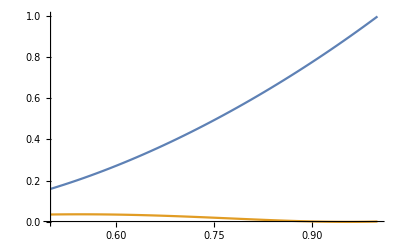

```mathematica
Subscript[z, h]=1;
(*sl=F1H[c1,c2, ω,k][bound]//.result/.k->1/.c1->1//Quiet
sl1=F2H[czx,czy,vzx,vzy, ω,k][bound]/.k->1/.result//Quiet*)
Show[Plot[{htx[z]/.sl1//Re,htx[z]/.sl1//Im},{z,bound,zh},PlotRange->All](*,Plot[{hzx[z]/.sl2//Re,hzx[z]/.sl2//Im},{z,0,bound},PlotRange->All]*),PlotRange->All]/.zh->Subscript[z, h]//Quiet
```

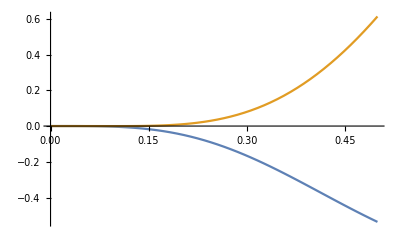

```mathematica
Show[(*Plot[{hzx[z]/.sl1//Re,hzx[z]/.sl1//Im},{z,bound,zh},PlotRange->All]*)Plot[{hzx[z]/.sl2//Re,hzx[z]/.sl2//Im},{z,0,bound},PlotRange->All],PlotRange->All]/.zh->Subscript[z, h]//Quiet
```

```mathematica
(*Extract the interpolation data points from f1 and f2*)
datahtx1=Table[{z,htx[z]/.sl2},{z,small,bound,(*choose an appropriate step size,e.g.,*)0.001}];
datahtx2=Table[{z,htx[z]/.sl1},{z,bound+0.01,1-smallIR,0.001}]; (*avoid redundancy at z=b*)

(*Combine the data from both interpolations*)
combinedDatahtx=Join[datahtx1,datahtx2];

(*Create a new interpolation function from the combined data*)
(*htxFunction2[z_]=Interpolation[combinedDatahtx//Transpose];*)
```

```mathematica
htxFunction[z_]:=Piecewise[{{htx[z]/.sl2,z<bound},{htx[z]/.sl1,z>=bound}}];
hzxFunction[z_]:=Piecewise[{{hzx[z]/.sl2,z<bound},{hzx[z]/.sl1,z>=bound}}];
```

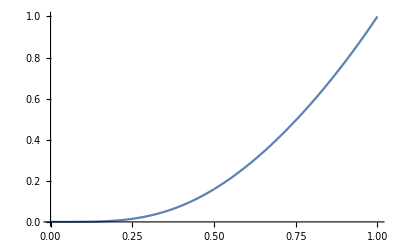

```mathematica
Plot[{(*htxFunction[z]//Re,*)htxFunction[z]//Re},{z,0,1},PlotRange->All]
```

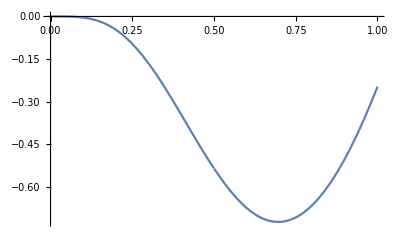

```mathematica
Plot[{hzxFunction[z]//Re(*,hzxFunction[z]//Im*)},{z,0,1},PlotRange->All]
```

### Energy Computation

```mathematica
hhtxNorm=1;
hhzxNorm=1;
```

#### htx And hzx

(ⅇ^(ⅈ k x3-ⅈ v ω) ϵ htx[z])/(2 z^2)

```mathematica
(*htx[v_,z_,x3_]=1/(2 z^2)htxFunction[z] E^(-I ω v+I k x3)/.k->1/.result;
hzx[v_,z_,x3_]=1/(2 z^2)hzxFunction[z] E^(-I ω v+I k x3)/.k->1/.result;*)
```

```mathematica
ClearAll[hzx]
```

#### Master Scalar

```mathematica
gdd=G/.ϵ->0;
```

```mathematica
guu=IG/.ϵ->0;
```

```mathematica
ΓBG=Γ/.ϵ->0;
```

```mathematica
ClearAll[Φ]
```

```mathematica
CovCov=Sum[guu[[a,b]](D[D[Φ[v,z,x3], X[[a]]], X[[b]]]-Sum[Γ[[e,b,a]]D[Φ[v,z,x3], X[[e]]],{e,1,5}]),{a,1,5},{b,1,5}]//Simplify;
```

Eq 3.9, W_(2,2) , the other Ws are zero.
Note that the r derivative has to be changed in accordance to the expression in appendix D2, just before equations D6

```mathematica
Pot=k^2 z^2-3(-z^2 D[f[z], z]z-f[z] z^2)(*k^2 z^2+z^2∂_z f[z]z+(-f[z] z^2)*);
```

```mathematica
MasterEq=CovCov-(*V*)Pot Φ[v,z,x3](*/.k->1*);
```

```mathematica
Pot/.f->Function[z,1/z^2(1-z^4/zh^4)]//Series[#,{z,0,4}]&
```

-3+k^2 z^2-(9 z^4)/zh^4+O[z]^5

```mathematica
MasterEq
```

-Φ[v,z,x3] (k^2 z^2-3 (-z^2 f[z]-z^3 f'[z]))+z (z Φ^(0,0,2)[v,z,x3]+z^3 f'[z] Φ^(0,1,0)[v,z,x3]+z^2 f[z] (-Φ^(0,1,0)[v,z,x3]+z Φ^(0,2,0)[v,z,x3])+3 Φ^(1,0,0)[v,z,x3]-2 z Φ^(1,1,0)[v,z,x3])

```mathematica
Pot
```

k^2 z^2-3 (-z^2 f[z]-z^3 f'[z])

#### EF to FG

```mathematica
XFG={v+ Integrate[1/f[z],z],z,x1,x2,x3}
```

{v+∫1/f[z]ⅆz,z,x1,x2,x3}

```mathematica
X
```

{v,z,x1,x2,x3}

```mathematica
JacobianFG=Table[D[XFG[[i]],X[[j]]],{i,1,5},{j,1,5}]; (*This computes a 5x5 Jacobian matrix*)
```

```mathematica
JacobianFG
```

{{1,1/f[z],0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

```mathematica
GFG=Table[Sum[JacobianFG[[u,a]] G[[u,vv]] JacobianFG[[vv,b]],{u,1,5},{vv,1,5}],{a,1,5},{b,1,5}]//Simplify;
GFGh=SeriesCoefficient[GFG,{ϵ,0,1}]//Normal;
GFGh//MatrixForm
```

(0 | 0 | (ⅇ^(ⅈ (k x3-v ω)) htx[z])/(2 z^2) | 0 | 0
0 | 0 | (ⅇ^(ⅈ (k x3-v ω)) htx[z])/(2 z^2 f[z]) | 0 | 0
(ⅇ^(ⅈ (k x3-v ω)) htx[z])/(2 z^2) | (ⅇ^(ⅈ (k x3-v ω)) htx[z])/(2 z^2 f[z]) | 0 | 0 | (ⅇ^(ⅈ (k x3-v ω)) hzx[z])/(2 z^2)
0 | 0 | 0 | 0 | 0
0 | 0 | (ⅇ^(ⅈ (k x3-v ω)) hzx[z])/(2 z^2) | 0 | 0)

#### H Curly FG

Already translated 
Eq D4

```mathematica
HFGtz=GFGh[[1,3]]-D[GFGh[[3,5]]/(I k), v]//Simplify;
HFGrz=GFGh[[2,3]]+(z^2 D[GFGh[[3,5]]/(I k), z]-1/f[z] D[GFGh[[3,5]]/(I k), v])+2z GFGh[[3,5]]/(I k)//Simplify;
```

#### H Curly EF

Eq D4

```mathematica
HEFtz=HFGtz;
HEFrz=HFGrz-1/f[z] HFGtz;
```

#### Boundary conditions

```mathematica
Normal[Series[MasterEq/.Φ->Function[{v,z,x3},E^(-I ω v) z^(Δ(*-1/2*))]/.f->Function[z,1/z^2(1-z^4/zh^4)]/.k->N[2 Pi/L,56]/.ω->0/.zh->1,{z,0,1}]]//Simplify
```

z^Δ (3-4 Δ+Δ^2)

```mathematica
Solve[%==0,Δ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Δ→1},{Δ→3}}

I take the asymptotic expansions and define the asymptotic exp of the whole perturbations

```mathematica
ΦExp=Function[z, Sum[p[i] z^i,{i,1,7}]];
```

```mathematica
hhtxExp=hhtxNorm(ⅇ^(ⅈ k x3-ⅈ v ω) Ashtx[czx,vzx, ω,k][z])/(2 z^2)(*/.result*);
hhzxExp=hhzxNorm(ⅇ^(ⅈ k x3-ⅈ v ω) Ashzx[czx,vzx, ω,k][z])/(2 z^2)(*/.result*);
```

To check

Eq. D6

```mathematica
hEFrzEXP=HEFrz/.hzx->Function[z,hhzxNorm Ashzx[czx,vzx, ω,k][z]]/.htx->Function[z,hhtxNorm Ashtx[czx,vzx, ω,k][z]](*z^2∂_z hhzxExp(I k)^-1+2 z hhzxExp(I k)^-1-1/f[z](hhtxExp-∂_v hhzxExp(I k)^-1)*)/.f->Function[z,1/z^2(1-z^4/zh^4)]/.zh->1(*/.k->1*);
EXPEq=hEFrzEXP==(ⅇ^(ⅈ k x3-ⅈ v ω)D[ΦExp[z], z]-3/z ⅇ^(ⅈ k x3-ⅈ v ω)ΦExp[z]);
```

```mathematica
(*z^2∂_z hhzxExp+2 z hhzxExp-1/f[z](hhtxExp-∂_v hhzxExp)==(HEFrz/.hzx->Function[z,Ashzx[czx,vzx, ω,k][z]]/.htx->Function[z,Ashtx[czx,vzx, ω,k][z]])/.f->Function[z,1/z^2(1-z^4/zh^4)]/.zh->1//Simplify*)
```

```mathematica
EXPEq2=(HEFtz/.hzx->Function[z,Ashzx[czx,vzx, ω,k][z]]/.htx->Function[z,Ashtx[czx,vzx, ω,k][z]])(*hhtxExp-∂_v hhzxExp*)==3 f[z]/z ⅇ^(ⅈ k x3-ⅈ v ω)ΦExp[z]+f[z]/z^2(-z^2 D[(ⅇ^(ⅈ k x3-ⅈ v ω)ΦExp[z]), z])+1/z^2 D[(ⅇ^(ⅈ k x3-ⅈ v ω)ΦExp[z]), v]/.f->Function[z,1/z^2(1-z^4/zh^4)]/.zh->1;
```

```mathematica
p1Rule=Solve[Series[{EXPEq},{z,0,0}]//Normal,p[1]]//Flatten(*//Simplify*)
```

{p[1]→0}

```mathematica
Solve[Series[EXPEq2,{z,0,-2}]//Normal,p[1]]//Flatten(*//Simplify*)
```

{p[1]→0}

```mathematica
p2Rule=Solve[Series[EXPEq,{z,0,1}]/.p1Rule//Normal,p[2]]//Flatten
```

{p[2]→0}

```mathematica
Solve[Series[EXPEq2,{z,0,-1}]/.p1Rule//Normal,p[2]]//Flatten
```

{p[2]→0}

```mathematica
Solve[Series[EXPEq,{z,0,2}]/.p1Rule/.p2Rule//Normal,p[3]]//Flatten
```

{}

```mathematica
p4Rule=Solve[Series[EXPEq,{z,0,3}](*/.p3Rule*)/.p1Rule/.p2Rule//Normal,p[4]]//Flatten
```

{p[4]→(2 ⅈ vzx ω)/k^2}

```mathematica
p5Rule=Solve[Series[EXPEq,{z,0,4}]/.p4Rule/.p1Rule/.p2Rule(*/.p3Rule*)//Normal,p[5]]//Flatten
```

{p[5]→-(vzx (k^2-5 ω^2))/(4 k^2)}

```mathematica
p6Rule=Solve[Series[EXPEq,{z,0,5}]/.p5Rule/.p1Rule/.p2Rule(*/.p3Rule*)/.p4Rule//Normal,p[6]]//Simplify//Flatten
```

{p[6]→(ⅈ vzx ω (3 k^2-7 ω^2))/(12 k^2)}

```mathematica
p7Rule=Solve[Series[EXPEq,{z,0,6}]/.p6Rule/.p1Rule/.p2Rule(*/.p3Rule*)/.p4Rule/.p5Rule//Normal,p[7]](*/.result/.k->1*)//Simplify//Flatten
```

{p[7]→0}

```mathematica
p3Rule=Solve[Series[EXPEq2,{z,0,1}]/.p1Rule/.p2Rule/.p4Rule//Normal,p[3]]//Flatten(*//Simplify*)
```

{p[3]→-(2 vzx)/k^2}

consistency check

```mathematica
Series[EXPEq2,{z,0,1}]/.p1Rule/.p2Rule/.p3Rule/.p4Rule//Normal
```

True

```mathematica
Series[EXPEq2,{z,0,2}]/.p1Rule/.p2Rule/.p3Rule/.p4Rule/.p5Rule//Normal//Simplify
```

True

```mathematica
Series[EXPEq2,{z,0,2}]/.p1Rule/.p2Rule/.p3Rule/.p4Rule/.p5Rule//Normal//Simplify
```

True

```mathematica
Series[EXPEq2,{z,0,3}]/.p1Rule/.p2Rule/.p3Rule/.p4Rule/.p5Rule/.p6Rule//Normal//Simplify
```

True

```mathematica
(*p7Rule=Solve[Series[EXPEq,{z,0,6}]/.p0Rule/.p1Rule/.p2Rule/.p3Rule/.p4Rule/.p5Rule/.p6Rule//Normal,p[7]](*/.result/.k->1*)//Simplify//Flatten*)
```

```mathematica
(*p8Rule=Solve[Series[EXPEq,{z,0,7}]/.p0Rule/.p1Rule/.p2Rule/.p3Rule/.p4Rule/.p5Rule/.p6Rule/.p7Rule//Normal,p[8]](*/.result/.k->1*)//Simplify//Flatten*)
```

```mathematica
(*p9Rule=Solve[Series[EXPEq,{z,0,8}]/.p0Rule/.p1Rule/.p2Rule/.p3Rule/.p4Rule/.p5Rule/.p6Rule/.p7Rule/.p8Rule//Normal,p[9]](*/.result/.k->1*)//Simplify//Flatten*)
```

```mathematica
ClearAll[ΦExpBC]
```

```mathematica
ΦExpBC[zz_]:=ΦExp[z]/.p1Rule/.p2Rule/.p3Rule/.p4Rule/.p5Rule/.p6Rule/.p7Rule/.result/.k->2 Pi/L/.z->zz
```

```mathematica
ΦExpBC[small]
```

-1.86531126743471534339827800399958501177540776641567921×10^-17-3.51744170598266146194162400853062163349523021732684284×10^-17 ⅈ

```mathematica
D[ΦExpBC[z], z]/.z->small
```

-5.59593983987711529034565444629091196901171359270234964×10^-11-1.05523096022899830495967966728504960909486656421300048×10^-10 ⅈ

#### Differential Equation for Φ

```mathematica
hhzx[v_,z_,x3_]:=hhzxNorm ⅇ^(ⅈ k x3-ⅈ v ω)/(2 z^2)hzxFunction[z];
hhtx[v_,z_,x3_]:=hhtxNorm ⅇ^(ⅈ k x3-ⅈ v ω)/(2 z^2)htxFunction[z];
```

```mathematica
(*ClearAll[hhzx,hhtx]*)
```

```mathematica
(*z^2∂_z hhzxExp(I k)^-1+2 z hhzxExp(I k)^-1-1/f[z](hhtxExp-∂_v hhzxExp(I k)^-1)*)
```

```mathematica
HEFrz
```

-(ⅇ^(ⅈ (k x3-v ω)) (k htx[z]+ω hzx[z]))/(2 k z^2 f[z])+(ⅇ^(ⅈ (k x3-v ω)) (k htx[z]+ω hzx[z]-ⅈ z^2 f[z] hzx'[z]))/(2 k z^2 f[z])

```mathematica
ΦEqLHS=HEFrz/.htx->Function[z,hhtxNorm htxFunction[z]]/.hzx->Function[z,hhzxNorm hzxFunction[z]]/.f->Function[z,1/z^2(1-z^4/zh^4)]/.zh->1(*/.k->1*);
ΦEqRHS=(ⅇ^(ⅈ k x3-ⅈ v ω)D[(z^3 Φ[z]), z]-3/z ⅇ^(ⅈ k x3-ⅈ v ω)(z^3 Φ[z]))/.f->Function[z,1/z^2(1-z^4/zh^4)]/.zh->1/.k->2 Pi/L(*/.x3->0*)/.v->0(*/.ω->0*)/.result(*//Simplify*);
```

```mathematica
ΦEq=(ΦEqLHS/.zh->1/.k->2 Pi/L/.x3->0/.v->0/.result)==(ΦEqRHS/.zh->1/.k->2 Pi/L/.x3->0/.v->0/.result);
```

```mathematica
ΦEqRHS
```

-3 ⅇ^((ⅈ π x3)/5) z^2 Φ[z]+ⅇ^((ⅈ π x3)/5) (3 z^2 Φ[z]+z^3 Φ'[z])

```mathematica
ΦFunction=Φ/.(NDSolve[{ΦEq,(Φ[small]==ΦExpBC[small]/small^3)(*,Φ'[small]==∂_z ΦExpBC[z]/.z->small*)},Φ,{z,small,1-smallIR},WorkingPrecision->30]//Flatten)
```

-6
InterpolatingFunction[{{1.00000000000000000000000000000 10  , 0.99999999990000000000000000000}}, <>]

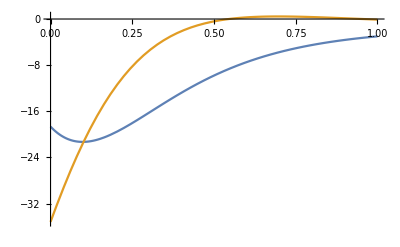

```mathematica
Plot[{(ΦFunction[z])//Re,(ΦFunction[z])//Im},{z,0,1},PlotRange->All]
```

#### Energy

```mathematica
ClearAll[Tdd]
```

```mathematica
Tdd=Table[1/2 D[(ⅇ^(ⅈ k x3-ⅈ v ω)z^3 Φ[z]), X[[a]]](Conjugate[D[(z^3 ⅇ^(ⅈ k x3-ⅈ v ω)Φ[z]), X[[b]]]])+1/2 1/2  (Conjugate[D[(z^3 ⅇ^(ⅈ k x3-ⅈ v ω) Φ[z]), X[[a]]]])D[(ⅇ^(ⅈ k x3-ⅈ v ω)z^3 Φ[z]), X[[b]]]-(G[[a,b]]/.ϵ->0)(Sum[IG[[c,cc]]D[(ⅇ^(ⅈ k x3-ⅈ v ω)z^3 Φ[z]), X[[c]]](Conjugate[D[(z^3 ⅇ^(ⅈ k x3-ⅈ v ω) Φ[z]), X[[cc]]]]),{cc,1,5},{c,1,5}]+Pot ⅇ^(ⅈ k x3-ⅈ v ω)z^3 Φ[z] z^3 (Conjugate[ⅇ^(ⅈ k x3-ⅈ v ω)Φ[z]])),{a,1,5},{b,1,5}]/.result/.k->2 Pi/L(*/.x3->0*)/.v->0/.ϵ->0/.f->Function[z,1/z^2(1-z^4/zh^4)]/.zh->1/. Φ->Function[z,ΦFunction[z]];
```

I define a tangent vector ξ coming from (∂x^μ)/(∂λ) (where in the parametrization x^μ=0,λ,0,0,0) and the surface element dΣ_μ=r^2 dr dx_1 dx_2 dx_3∂_μ Φ, where Φ is the equation of the hypersurface Φ=v-constant=0. So dΣ_μ is going to be in the direction of v. Then I convert  r=1/z and dr=-1/z^2 dz

```mathematica
ξu={0,1,0,0,0};
dΣu=-1/z^4 IG.{1,0,0,0,0}/.ϵ->0;
```

```mathematica
G.ξu.dΣu/.f->Function[z,1/z^2(1-z^4/zh^4)]/.ϵ->0//Simplify
```

0

```mathematica
ClearAll[Integrand]
```

```mathematica
Integrand[zz_]:=Sum[Tdd[[a,b]]ξu[[a]]dΣu[[b]]/.f->Function[z,1/z^2(1-z^4/zh^4)]/.v->0/.zh->1/.k->2 Pi/L(*/.x3->0*),{a,1,5},{b,1,5}]/.result/.z->zz//Simplify
```

```mathematica
Integrand[z]
```

3/4 ⅇ^(1/5 ⅈ π (x3-Conjugate[x3])) Conjugate[z]^2 (3 Conjugate[                                                          -6
InterpolatingFunction[{{1.00000000000000000000000000000 10  , 0.99999999990000000000000000000}}, <>][z]]+Conjugate[z                                                           -6
InterpolatingFunction[{{1.00000000000000000000000000000 10  , 0.99999999990000000000000000000}}, <>][z]]) (3                                                           -6
InterpolatingFunction[{{1.00000000000000000000000000000 10  , 0.99999999990000000000000000000}}, <>][z]+z                                                           -6
InterpolatingFunction[{{1.00000000000000000000000000000 10  , 0.99999999990000000000000000000}}, <>][z])

Below I compute the energy per spatial voume. It ha s to be multiplied by a factor L^3

```mathematica
PertEN=NIntegrate[(*Abs[*)Integrand[z](*]*),{z,0,1},{x3,-5,5},{x1,-5,5},{x2,-5,5}]
```

45962.

Check that ξ and dΣ are orthogonal

The energy scales as the norm factor squared.

```mathematica
NormFactor=1000
```

1000

```mathematica
NormFactor^-2 PertEN//N
```

0.045962

```mathematica
NormFactor=Abs[A/.Solve[0.99==1-1/A^2 PertEN,A][[1]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

2143.87

```mathematica
(PertEN/NormFactor^2)^(1/4)
```

0.316228

with r_h=1, this perturbation contains a fraction of th energy corresponding to the percentage:

```mathematica
% 100
```

31.6228